```mathematica
Integrate
```

```mathematica
fun=Integrate[1/Times@@Array[x-Subscript[a,#]&,#],x]&
```

∫1/(Times@@Array[x-a_#1&,#1])ⅆx&

```mathematica
Array[fun,5]//Together//TableForm
```

Log[x-a_1]
(Log[x-a_1]-Log[x-a_2])/(a_1-a_2)
(-Log[x-a_2] a_1+Log[x-a_3] a_1+Log[x-a_1] a_2-Log[x-a_3] a_2-Log[x-a_1] a_3+Log[x-a_2] a_3)/((a_1-a_2) (a_1-a_3) (a_2-a_3))
(Log[x-a_3] a_1^2 a_2-Log[x-a_4] a_1^2 a_2-Log[x-a_3] a_1 a_2^2+Log[x-a_4] a_1 a_2^2-Log[x-a_2] a_1^2 a_3+Log[x-a_4] a_1^2 a_3+Log[x-a_1] a_2^2 a_3-Log[x-a_4] a_2^2 a_3+Log[x-a_2] a_1 a_3^2-Log[x-a_4] a_1 a_3^2-Log[x-a_1] a_2 a_3^2+Log[x-a_4] a_2 a_3^2+Log[x-a_2] a_1^2 a_4-Log[x-a_3] a_1^2 a_4-Log[x-a_1] a_2^2 a_4+Log[x-a_3] a_2^2 a_4+Log[x-a_1] a_3^2 a_4-Log[x-a_2] a_3^2 a_4-Log[x-a_2] a_1 a_4^2+Log[x-a_3] a_1 a_4^2+Log[x-a_1] a_2 a_4^2-Log[x-a_3] a_2 a_4^2-Log[x-a_1] a_3 a_4^2+Log[x-a_2] a_3 a_4^2)/((a_1-a_2) (a_1-a_3) (a_2-a_3) (a_1-a_4) (a_2-a_4) (a_3-a_4))
(-Log[x-a_4] a_1^3 a_2^2 a_3+Log[x-a_5] a_1^3 a_2^2 a_3+Log[x-a_4] a_1^2 a_2^3 a_3-Log[x-a_5] a_1^2 a_2^3 a_3+Log[x-a_4] a_1^3 a_2 a_3^2-Log[x-a_5] a_1^3 a_2 a_3^2-Log[x-a_4] a_1 a_2^3 a_3^2+Log[x-a_5] a_1 a_2^3 a_3^2-Log[x-a_4] a_1^2 a_2 a_3^3+Log[x-a_5] a_1^2 a_2 a_3^3+Log[x-a_4] a_1 a_2^2 a_3^3-Log[x-a_5] a_1 a_2^2 a_3^3+Log[x-a_3] a_1^3 a_2^2 a_4-Log[x-a_5] a_1^3 a_2^2 a_4-Log[x-a_3] a_1^2 a_2^3 a_4+Log[x-a_5] a_1^2 a_2^3 a_4-Log[x-a_2] a_1^3 a_3^2 a_4+Log[x-a_5] a_1^3 a_3^2 a_4+Log[x-a_1] a_2^3 a_3^2 a_4-Log[x-a_5] a_2^3 a_3^2 a_4+Log[x-a_2] a_1^2 a_3^3 a_4-Log[x-a_5] a_1^2 a_3^3 a_4-Log[x-a_1] a_2^2 a_3^3 a_4+Log[x-a_5] a_2^2 a_3^3 a_4-Log[x-a_3] a_1^3 a_2 a_4^2+Log[x-a_5] a_1^3 a_2 a_4^2+Log[x-a_3] a_1 a_2^3 a_4^2-Log[x-a_5] a_1 a_2^3 a_4^2+Log[x-a_2] a_1^3 a_3 a_4^2-Log[x-a_5] a_1^3 a_3 a_4^2-Log[x-a_1] a_2^3 a_3 a_4^2+Log[x-a_5] a_2^3 a_3 a_4^2-Log[x-a_2] a_1 a_3^3 a_4^2+Log[x-a_5] a_1 a_3^3 a_4^2+Log[x-a_1] a_2 a_3^3 a_4^2-Log[x-a_5] a_2 a_3^3 a_4^2+Log[x-a_3] a_1^2 a_2 a_4^3-Log[x-a_5] a_1^2 a_2 a_4^3-Log[x-a_3] a_1 a_2^2 a_4^3+Log[x-a_5] a_1 a_2^2 a_4^3-Log[x-a_2] a_1^2 a_3 a_4^3+Log[x-a_5] a_1^2 a_3 a_4^3+Log[x-a_1] a_2^2 a_3 a_4^3-Log[x-a_5] a_2^2 a_3 a_4^3+Log[x-a_2] a_1 a_3^2 a_4^3-Log[x-a_5] a_1 a_3^2 a_4^3-Log[x-a_1] a_2 a_3^2 a_4^3+Log[x-a_5] a_2 a_3^2 a_4^3-Log[x-a_3] a_1^3 a_2^2 a_5+Log[x-a_4] a_1^3 a_2^2 a_5+Log[x-a_3] a_1^2 a_2^3 a_5-Log[x-a_4] a_1^2 a_2^3 a_5+Log[x-a_2] a_1^3 a_3^2 a_5-Log[x-a_4] a_1^3 a_3^2 a_5-Log[x-a_1] a_2^3 a_3^2 a_5+Log[x-a_4] a_2^3 a_3^2 a_5-Log[x-a_2] a_1^2 a_3^3 a_5+Log[x-a_4] a_1^2 a_3^3 a_5+Log[x-a_1] a_2^2 a_3^3 a_5-Log[x-a_4] a_2^2 a_3^3 a_5-Log[x-a_2] a_1^3 a_4^2 a_5+Log[x-a_3] a_1^3 a_4^2 a_5+Log[x-a_1] a_2^3 a_4^2 a_5-Log[x-a_3] a_2^3 a_4^2 a_5-Log[x-a_1] a_3^3 a_4^2 a_5+Log[x-a_2] a_3^3 a_4^2 a_5+Log[x-a_2] a_1^2 a_4^3 a_5-Log[x-a_3] a_1^2 a_4^3 a_5-Log[x-a_1] a_2^2 a_4^3 a_5+Log[x-a_3] a_2^2 a_4^3 a_5+Log[x-a_1] a_3^2 a_4^3 a_5-Log[x-a_2] a_3^2 a_4^3 a_5+Log[x-a_3] a_1^3 a_2 a_5^2-Log[x-a_4] a_1^3 a_2 a_5^2-Log[x-a_3] a_1 a_2^3 a_5^2+Log[x-a_4] a_1 a_2^3 a_5^2-Log[x-a_2] a_1^3 a_3 a_5^2+Log[x-a_4] a_1^3 a_3 a_5^2+Log[x-a_1] a_2^3 a_3 a_5^2-Log[x-a_4] a_2^3 a_3 a_5^2+Log[x-a_2] a_1 a_3^3 a_5^2-Log[x-a_4] a_1 a_3^3 a_5^2-Log[x-a_1] a_2 a_3^3 a_5^2+Log[x-a_4] a_2 a_3^3 a_5^2+Log[x-a_2] a_1^3 a_4 a_5^2-Log[x-a_3] a_1^3 a_4 a_5^2-Log[x-a_1] a_2^3 a_4 a_5^2+Log[x-a_3] a_2^3 a_4 a_5^2+Log[x-a_1] a_3^3 a_4 a_5^2-Log[x-a_2] a_3^3 a_4 a_5^2-Log[x-a_2] a_1 a_4^3 a_5^2+Log[x-a_3] a_1 a_4^3 a_5^2+Log[x-a_1] a_2 a_4^3 a_5^2-Log[x-a_3] a_2 a_4^3 a_5^2-Log[x-a_1] a_3 a_4^3 a_5^2+Log[x-a_2] a_3 a_4^3 a_5^2-Log[x-a_3] a_1^2 a_2 a_5^3+Log[x-a_4] a_1^2 a_2 a_5^3+Log[x-a_3] a_1 a_2^2 a_5^3-Log[x-a_4] a_1 a_2^2 a_5^3+Log[x-a_2] a_1^2 a_3 a_5^3-Log[x-a_4] a_1^2 a_3 a_5^3-Log[x-a_1] a_2^2 a_3 a_5^3+Log[x-a_4] a_2^2 a_3 a_5^3-Log[x-a_2] a_1 a_3^2 a_5^3+Log[x-a_4] a_1 a_3^2 a_5^3+Log[x-a_1] a_2 a_3^2 a_5^3-Log[x-a_4] a_2 a_3^2 a_5^3-Log[x-a_2] a_1^2 a_4 a_5^3+Log[x-a_3] a_1^2 a_4 a_5^3+Log[x-a_1] a_2^2 a_4 a_5^3-Log[x-a_3] a_2^2 a_4 a_5^3-Log[x-a_1] a_3^2 a_4 a_5^3+Log[x-a_2] a_3^2 a_4 a_5^3+Log[x-a_2] a_1 a_4^2 a_5^3-Log[x-a_3] a_1 a_4^2 a_5^3-Log[x-a_1] a_2 a_4^2 a_5^3+Log[x-a_3] a_2 a_4^2 a_5^3+Log[x-a_1] a_3 a_4^2 a_5^3-Log[x-a_2] a_3 a_4^2 a_5^3)/((a_1-a_2) (a_1-a_3) (a_2-a_3) (a_1-a_4) (a_2-a_4) (a_3-a_4) (a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))

```mathematica
Collect[%58[[-1]]//Numerator,Log[x-_]]
```

Log[x-a_5] (a_1^3 a_2^2 a_3-a_1^2 a_2^3 a_3-a_1^3 a_2 a_3^2+a_1 a_2^3 a_3^2+a_1^2 a_2 a_3^3-a_1 a_2^2 a_3^3-a_1^3 a_2^2 a_4+a_1^2 a_2^3 a_4+a_1^3 a_3^2 a_4-a_2^3 a_3^2 a_4-a_1^2 a_3^3 a_4+a_2^2 a_3^3 a_4+a_1^3 a_2 a_4^2-a_1 a_2^3 a_4^2-a_1^3 a_3 a_4^2+a_2^3 a_3 a_4^2+a_1 a_3^3 a_4^2-a_2 a_3^3 a_4^2-a_1^2 a_2 a_4^3+a_1 a_2^2 a_4^3+a_1^2 a_3 a_4^3-a_2^2 a_3 a_4^3-a_1 a_3^2 a_4^3+a_2 a_3^2 a_4^3)+Log[x-a_4] (-a_1^3 a_2^2 a_3+a_1^2 a_2^3 a_3+a_1^3 a_2 a_3^2-a_1 a_2^3 a_3^2-a_1^2 a_2 a_3^3+a_1 a_2^2 a_3^3+a_1^3 a_2^2 a_5-a_1^2 a_2^3 a_5-a_1^3 a_3^2 a_5+a_2^3 a_3^2 a_5+a_1^2 a_3^3 a_5-a_2^2 a_3^3 a_5-a_1^3 a_2 a_5^2+a_1 a_2^3 a_5^2+a_1^3 a_3 a_5^2-a_2^3 a_3 a_5^2-a_1 a_3^3 a_5^2+a_2 a_3^3 a_5^2+a_1^2 a_2 a_5^3-a_1 a_2^2 a_5^3-a_1^2 a_3 a_5^3+a_2^2 a_3 a_5^3+a_1 a_3^2 a_5^3-a_2 a_3^2 a_5^3)+Log[x-a_3] (a_1^3 a_2^2 a_4-a_1^2 a_2^3 a_4-a_1^3 a_2 a_4^2+a_1 a_2^3 a_4^2+a_1^2 a_2 a_4^3-a_1 a_2^2 a_4^3-a_1^3 a_2^2 a_5+a_1^2 a_2^3 a_5+a_1^3 a_4^2 a_5-a_2^3 a_4^2 a_5-a_1^2 a_4^3 a_5+a_2^2 a_4^3 a_5+a_1^3 a_2 a_5^2-a_1 a_2^3 a_5^2-a_1^3 a_4 a_5^2+a_2^3 a_4 a_5^2+a_1 a_4^3 a_5^2-a_2 a_4^3 a_5^2-a_1^2 a_2 a_5^3+a_1 a_2^2 a_5^3+a_1^2 a_4 a_5^3-a_2^2 a_4 a_5^3-a_1 a_4^2 a_5^3+a_2 a_4^2 a_5^3)+Log[x-a_2] (-a_1^3 a_3^2 a_4+a_1^2 a_3^3 a_4+a_1^3 a_3 a_4^2-a_1 a_3^3 a_4^2-a_1^2 a_3 a_4^3+a_1 a_3^2 a_4^3+a_1^3 a_3^2 a_5-a_1^2 a_3^3 a_5-a_1^3 a_4^2 a_5+a_3^3 a_4^2 a_5+a_1^2 a_4^3 a_5-a_3^2 a_4^3 a_5-a_1^3 a_3 a_5^2+a_1 a_3^3 a_5^2+a_1^3 a_4 a_5^2-a_3^3 a_4 a_5^2-a_1 a_4^3 a_5^2+a_3 a_4^3 a_5^2+a_1^2 a_3 a_5^3-a_1 a_3^2 a_5^3-a_1^2 a_4 a_5^3+a_3^2 a_4 a_5^3+a_1 a_4^2 a_5^3-a_3 a_4^2 a_5^3)+Log[x-a_1] (a_2^3 a_3^2 a_4-a_2^2 a_3^3 a_4-a_2^3 a_3 a_4^2+a_2 a_3^3 a_4^2+a_2^2 a_3 a_4^3-a_2 a_3^2 a_4^3-a_2^3 a_3^2 a_5+a_2^2 a_3^3 a_5+a_2^3 a_4^2 a_5-a_3^3 a_4^2 a_5-a_2^2 a_4^3 a_5+a_3^2 a_4^3 a_5+a_2^3 a_3 a_5^2-a_2 a_3^3 a_5^2-a_2^3 a_4 a_5^2+a_3^3 a_4 a_5^2+a_2 a_4^3 a_5^2-a_3 a_4^3 a_5^2-a_2^2 a_3 a_5^3+a_2 a_3^2 a_5^3+a_2^2 a_4 a_5^3-a_3^2 a_4 a_5^3-a_2 a_4^2 a_5^3+a_3 a_4^2 a_5^3)

```mathematica
(Subscript[a, 1]^3 Subscript[a, 2]^2 Subscript[a, 3]-Subscript[a, 1]^2 Subscript[a, 2]^3 Subscript[a, 3]-Subscript[a, 1]^3 Subscript[a, 2] Subscript[a, 3]^2+Subscript[a, 1] Subscript[a, 2]^3 Subscript[a, 3]^2+Subscript[a, 1]^2 Subscript[a, 2] Subscript[a, 3]^3-Subscript[a, 1] Subscript[a, 2]^2 Subscript[a, 3]^3-Subscript[a, 1]^3 Subscript[a, 2]^2 Subscript[a, 4]+Subscript[a, 1]^2 Subscript[a, 2]^3 Subscript[a, 4]+Subscript[a, 1]^3 Subscript[a, 3]^2 Subscript[a, 4]-Subscript[a, 2]^3 Subscript[a, 3]^2 Subscript[a, 4]-Subscript[a, 1]^2 Subscript[a, 3]^3 Subscript[a, 4]+Subscript[a, 2]^2 Subscript[a, 3]^3 Subscript[a, 4]+Subscript[a, 1]^3 Subscript[a, 2] Subscript[a, 4]^2-Subscript[a, 1] Subscript[a, 2]^3 Subscript[a, 4]^2-Subscript[a, 1]^3 Subscript[a, 3] Subscript[a, 4]^2+Subscript[a, 2]^3 Subscript[a, 3] Subscript[a, 4]^2+Subscript[a, 1] Subscript[a, 3]^3 Subscript[a, 4]^2-Subscript[a, 2] Subscript[a, 3]^3 Subscript[a, 4]^2-Subscript[a, 1]^2 Subscript[a, 2] Subscript[a, 4]^3+Subscript[a, 1] Subscript[a, 2]^2 Subscript[a, 4]^3+Subscript[a, 1]^2 Subscript[a, 3] Subscript[a, 4]^3-Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 4]^3-Subscript[a, 1] Subscript[a, 3]^2 Subscript[a, 4]^3+Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 4]^3)//FullSimplify
```

(a_1-a_2) (a_1-a_3) (a_2-a_3) (a_1-a_4) (a_2-a_4) (a_3-a_4)

```mathematica
(-Subscript[a, 1]^3 Subscript[a, 2]^2 Subscript[a, 3]+Subscript[a, 1]^2 Subscript[a, 2]^3 Subscript[a, 3]+Subscript[a, 1]^3 Subscript[a, 2] Subscript[a, 3]^2-Subscript[a, 1] Subscript[a, 2]^3 Subscript[a, 3]^2-Subscript[a, 1]^2 Subscript[a, 2] Subscript[a, 3]^3+Subscript[a, 1] Subscript[a, 2]^2 Subscript[a, 3]^3+Subscript[a, 1]^3 Subscript[a, 2]^2 Subscript[a, 5]-Subscript[a, 1]^2 Subscript[a, 2]^3 Subscript[a, 5]-Subscript[a, 1]^3 Subscript[a, 3]^2 Subscript[a, 5]+Subscript[a, 2]^3 Subscript[a, 3]^2 Subscript[a, 5]+Subscript[a, 1]^2 Subscript[a, 3]^3 Subscript[a, 5]-Subscript[a, 2]^2 Subscript[a, 3]^3 Subscript[a, 5]-Subscript[a, 1]^3 Subscript[a, 2] Subscript[a, 5]^2+Subscript[a, 1] Subscript[a, 2]^3 Subscript[a, 5]^2+Subscript[a, 1]^3 Subscript[a, 3] Subscript[a, 5]^2-Subscript[a, 2]^3 Subscript[a, 3] Subscript[a, 5]^2-Subscript[a, 1] Subscript[a, 3]^3 Subscript[a, 5]^2+Subscript[a, 2] Subscript[a, 3]^3 Subscript[a, 5]^2+Subscript[a, 1]^2 Subscript[a, 2] Subscript[a, 5]^3-Subscript[a, 1] Subscript[a, 2]^2 Subscript[a, 5]^3-Subscript[a, 1]^2 Subscript[a, 3] Subscript[a, 5]^3+Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 5]^3+Subscript[a, 1] Subscript[a, 3]^2 Subscript[a, 5]^3-Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 5]^3)//FullSimplify
```

-(a_1-a_2) (a_1-a_3) (a_2-a_3) (a_1-a_5) (a_2-a_5) (a_3-a_5)

```mathematica
Table[Integrate[x^i/Times@@Array[x-Subscript[a,#]&,j],x],{i,0,5},{j,0,5}]
```

{{x,Log[x-a_1],(Log[x-a_1]-Log[x-a_2])/(a_1-a_2),(Log[x-a_3] (a_1-a_2)-Log[x-a_2] (a_1-a_3)+Log[x-a_1] (a_2-a_3))/((a_1-a_2) (a_1-a_3) (a_2-a_3)),Log[x-a_1]/((a_1-a_2) (a_1-a_3) (a_1-a_4))+Log[x-a_2]/((-a_1+a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3]/((a_1-a_3) (a_2-a_3))+Log[x-a_4]/((a_2-a_4) (-a_1+a_4)))/(a_3-a_4),Log[x-a_1]/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))+Log[x-a_2]/((-a_1+a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+Log[x-a_3]/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))+Log[x-a_4]/((a_2-a_4) (a_3-a_4) (-a_1+a_4) (a_4-a_5))+Log[x-a_5]/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))},{x^2/2,x+Log[x-a_1] a_1,(Log[x-a_1] a_1-Log[x-a_2] a_2)/(a_1-a_2),(-Log[x-a_2] a_2 (a_1-a_3)+Log[x-a_1] a_1 (a_2-a_3)+Log[x-a_3] (a_1-a_2) a_3)/((a_1-a_2) (a_1-a_3) (a_2-a_3)),(Log[x-a_1] a_1)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4),(Log[x-a_1] a_1)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))},{x^3/3,1/2 (x^2+2 x a_1+(-3+2 Log[x-a_1]) a_1^2),x+(Log[x-a_1] a_1^2)/(a_1-a_2)-(Log[x-a_2] a_2^2)/(a_1-a_2),(-Log[x-a_2] a_2^2 (a_1-a_3)+Log[x-a_1] a_1^2 (a_2-a_3)+Log[x-a_3] (a_1-a_2) a_3^2)/((a_1-a_2) (a_1-a_3) (a_2-a_3)),(Log[x-a_1] a_1^2)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^2)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3^2)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4^2)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4),(Log[x-a_1] a_1^2)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^2)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^2)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^2)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^2)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))},{x^4/4,1/6 (2 x^3+3 x^2 a_1+6 x a_1^2+(-11+6 Log[x-a_1]) a_1^3),1/2 (x-a_1)^2+(Log[x-a_1] a_1^3)/(a_1-a_2)-(Log[x-a_2] a_2^3)/(a_1-a_2)+(x-a_1) (2 a_1+a_2),x+(Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3)),(Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4^3)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4),(Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^3)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^3)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))},{x^5/5,1/12 (3 x^4+4 x^3 a_1+6 x^2 a_1^2+12 x a_1^3+(-25+12 Log[x-a_1]) a_1^4),1/3 (x-a_1)^3+(Log[x-a_1] a_1^4)/(a_1-a_2)-(Log[x-a_2] a_2^4)/(a_1-a_2)+1/2 (x-a_1)^2 (3 a_1+a_2)+(x-a_1) (3 a_1^2+2 a_1 a_2+a_2^2),1/2 (x-a_1)^2+(Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3))+(x-a_1) (2 a_1+a_2+a_3),x+(Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3) (a_3-a_4))-(Log[x-a_4] a_4^4)/((a_1-a_4) (a_2-a_4) (a_3-a_4)),(Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^4)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^4)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))},{x^6/6,x^5/5+(x^4 a_1)/4+1/3 x^3 a_1^2+1/2 x^2 a_1^3+x a_1^4+Log[x-a_1] a_1^5,(3 x^4 a_1+4 x^3 a_1^2+6 x^2 a_1^3+12 x a_1^4+12 Log[x-a_1] a_1^5-a_2 (3 x^4+4 x^3 a_2+6 x^2 a_2^2+12 x a_2^3+12 Log[x-a_2] a_2^4))/(12 (a_1-a_2)),1/3 (x-a_1)^3+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3))+1/2 (x-a_1)^2 (3 a_1+a_2+a_3)+(x-a_1) (3 a_1^2+a_2^2+a_2 a_3+a_3^2+2 a_1 (a_2+a_3)),1/2 (x-a_1)^2+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3) (a_3-a_4))-(Log[x-a_4] a_4^5)/((a_1-a_4) (a_2-a_4) (a_3-a_4))+(x-a_1) (2 a_1+a_2+a_3+a_4),x+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^5)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^5)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))}}

```mathematica
%67//MatrixForm
```

(x | Log[x-a_1] | (Log[x-a_1]-Log[x-a_2])/(a_1-a_2) | (Log[x-a_3] (a_1-a_2)-Log[x-a_2] (a_1-a_3)+Log[x-a_1] (a_2-a_3))/((a_1-a_2) (a_1-a_3) (a_2-a_3)) | Log[x-a_1]/((a_1-a_2) (a_1-a_3) (a_1-a_4))+Log[x-a_2]/((-a_1+a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3]/((a_1-a_3) (a_2-a_3))+Log[x-a_4]/((a_2-a_4) (-a_1+a_4)))/(a_3-a_4) | Log[x-a_1]/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))+Log[x-a_2]/((-a_1+a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+Log[x-a_3]/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))+Log[x-a_4]/((a_2-a_4) (a_3-a_4) (-a_1+a_4) (a_4-a_5))+Log[x-a_5]/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))
x^2/2 | x+Log[x-a_1] a_1 | (Log[x-a_1] a_1-Log[x-a_2] a_2)/(a_1-a_2) | (-Log[x-a_2] a_2 (a_1-a_3)+Log[x-a_1] a_1 (a_2-a_3)+Log[x-a_3] (a_1-a_2) a_3)/((a_1-a_2) (a_1-a_3) (a_2-a_3)) | (Log[x-a_1] a_1)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4) | (Log[x-a_1] a_1)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))
x^3/3 | 1/2 (x^2+2 x a_1+(-3+2 Log[x-a_1]) a_1^2) | x+(Log[x-a_1] a_1^2)/(a_1-a_2)-(Log[x-a_2] a_2^2)/(a_1-a_2) | (-Log[x-a_2] a_2^2 (a_1-a_3)+Log[x-a_1] a_1^2 (a_2-a_3)+Log[x-a_3] (a_1-a_2) a_3^2)/((a_1-a_2) (a_1-a_3) (a_2-a_3)) | (Log[x-a_1] a_1^2)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^2)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3^2)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4^2)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4) | (Log[x-a_1] a_1^2)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^2)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^2)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^2)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^2)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))
x^4/4 | 1/6 (2 x^3+3 x^2 a_1+6 x a_1^2+(-11+6 Log[x-a_1]) a_1^3) | 1/2 (x-a_1)^2+(Log[x-a_1] a_1^3)/(a_1-a_2)-(Log[x-a_2] a_2^3)/(a_1-a_2)+(x-a_1) (2 a_1+a_2) | x+(Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3)) | (Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+((Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3))+(Log[x-a_4] a_4^3)/((a_1-a_4) (-a_2+a_4)))/(a_3-a_4) | (Log[x-a_1] a_1^3)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^3)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^3)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^3)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^3)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))
x^5/5 | 1/12 (3 x^4+4 x^3 a_1+6 x^2 a_1^2+12 x a_1^3+(-25+12 Log[x-a_1]) a_1^4) | 1/3 (x-a_1)^3+(Log[x-a_1] a_1^4)/(a_1-a_2)-(Log[x-a_2] a_2^4)/(a_1-a_2)+1/2 (x-a_1)^2 (3 a_1+a_2)+(x-a_1) (3 a_1^2+2 a_1 a_2+a_2^2) | 1/2 (x-a_1)^2+(Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3))+(x-a_1) (2 a_1+a_2+a_3) | x+(Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3) (a_3-a_4))-(Log[x-a_4] a_4^4)/((a_1-a_4) (a_2-a_4) (a_3-a_4)) | (Log[x-a_1] a_1^4)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^4)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^4)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^4)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^4)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5))
x^6/6 | x^5/5+(x^4 a_1)/4+1/3 x^3 a_1^2+1/2 x^2 a_1^3+x a_1^4+Log[x-a_1] a_1^5 | (3 x^4 a_1+4 x^3 a_1^2+6 x^2 a_1^3+12 x a_1^4+12 Log[x-a_1] a_1^5-a_2 (3 x^4+4 x^3 a_2+6 x^2 a_2^2+12 x a_2^3+12 Log[x-a_2] a_2^4))/(12 (a_1-a_2)) | 1/3 (x-a_1)^3+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3))+1/2 (x-a_1)^2 (3 a_1+a_2+a_3)+(x-a_1) (3 a_1^2+a_2^2+a_2 a_3+a_3^2+2 a_1 (a_2+a_3)) | 1/2 (x-a_1)^2+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3) (a_1-a_4))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3) (a_2-a_4))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3) (a_3-a_4))-(Log[x-a_4] a_4^5)/((a_1-a_4) (a_2-a_4) (a_3-a_4))+(x-a_1) (2 a_1+a_2+a_3+a_4) | x+(Log[x-a_1] a_1^5)/((a_1-a_2) (a_1-a_3) (a_1-a_4) (a_1-a_5))-(Log[x-a_2] a_2^5)/((a_1-a_2) (a_2-a_3) (a_2-a_4) (a_2-a_5))+(Log[x-a_3] a_3^5)/((a_1-a_3) (a_2-a_3) (a_3-a_4) (a_3-a_5))-(Log[x-a_4] a_4^5)/((a_1-a_4) (a_2-a_4) (a_3-a_4) (a_4-a_5))+(Log[x-a_5] a_5^5)/((a_1-a_5) (a_2-a_5) (a_3-a_5) (a_4-a_5)))

```mathematica
Table[Integrate[x^i/Plus@@(x^Range[0,j]),x],{i,0,5},{j,0,5}]
```

{{x,Log[1+x],(2 ArcTan[(1+2 x)/(√3)])/(√3),ArcTan[x]/2+1/2 Log[1+x]-1/4 Log[1+x^2],RootSum[1+#1+#1^2+#1^3+#1^4&,Log[x-#1]/(1+2 #1+3 #1^2+4 #1^3)&],ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]},{x^2/2,x-Log[1+x],-ArcTan[(1+2 x)/(√3)]/(√3)+1/2 Log[1+x+x^2],ArcTan[x]/2-1/2 Log[1+x]+1/4 Log[1+x^2],RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1)/(1+2 #1+3 #1^2+4 #1^3)&],1/12 (2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]-4 Log[1+x]-Log[1-x+x^2]+3 Log[1+x+x^2])},{x^3/3,-2 (1+x)+1/2 (1+x)^2+Log[1+x],x-ArcTan[(1+2 x)/(√3)]/(√3)-1/2 Log[1+x+x^2],-ArcTan[x]/2+1/2 Log[1+x]+1/4 Log[1+x^2],RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1^2)/(1+2 #1+3 #1^2+4 #1^3)&],1/12 (2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]+4 Log[1+x]+Log[1-x+x^2]-3 Log[1+x+x^2])},{x^4/4,1/6 (11+6 x-3 x^2+2 x^3-6 Log[1+x]),-x+x^2/2+(2 ArcTan[(1+2 x)/(√3)])/(√3),x-ArcTan[x]/2-1/2 Log[1+x]-1/4 Log[1+x^2],RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1^3)/(1+2 #1+3 #1^2+4 #1^3)&],ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1+x]+1/6 Log[1-x+x^2]},{x^5/5,1/12 (-25-12 x+6 x^2-4 x^3+3 x^4+12 Log[1+x]),1/6 (x^2 (-3+2 x)-2 √3 ArcTan[(1+2 x)/(√3)]+3 Log[1+x+x^2]),-x+x^2/2+ArcTan[x]/2+1/2 Log[1+x]-1/4 Log[1+x^2],x-RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1]+Log[x-#1] #1+Log[x-#1] #1^2+Log[x-#1] #1^3)/(1+2 #1+3 #1^2+4 #1^3)&],1/12 (-2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]+4 Log[1+x]+Log[1-x+x^2]+3 Log[1+x+x^2])},{x^6/6,137/60+x-x^2/2+x^3/3-x^4/4+x^5/5-Log[1+x],x-x^3/3+x^4/4-ArcTan[(1+2 x)/(√3)]/(√3)-1/2 Log[1+x+x^2],-x^2/2+x^3/3+ArcTan[x]/2-1/2 Log[1+x]+1/4 Log[1+x^2],-x+x^2/2+RootSum[1+#1+#1^2+#1^3+#1^4&,Log[x-#1]/(1+2 #1+3 #1^2+4 #1^3)&],1/12 (12 x-2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]-4 Log[1+x]-Log[1-x+x^2]-3 Log[1+x+x^2])}}

```mathematica
%73//TableForm
```

x | Log[1+x] | (2 ArcTan[(1+2 x)/(√3)])/(√3) | ArcTan[x]/2+1/2 Log[1+x]-1/4 Log[1+x^2] | RootSum[1+#1+#1^2+#1^3+#1^4&,Log[x-#1]/(1+2 #1+3 #1^2+4 #1^3)&] | ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]
x^2/2 | x-Log[1+x] | -ArcTan[(1+2 x)/(√3)]/(√3)+1/2 Log[1+x+x^2] | ArcTan[x]/2-1/2 Log[1+x]+1/4 Log[1+x^2] | RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1)/(1+2 #1+3 #1^2+4 #1^3)&] | 1/12 (2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]-4 Log[1+x]-Log[1-x+x^2]+3 Log[1+x+x^2])
x^3/3 | -2 (1+x)+1/2 (1+x)^2+Log[1+x] | x-ArcTan[(1+2 x)/(√3)]/(√3)-1/2 Log[1+x+x^2] | -ArcTan[x]/2+1/2 Log[1+x]+1/4 Log[1+x^2] | RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1^2)/(1+2 #1+3 #1^2+4 #1^3)&] | 1/12 (2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]+4 Log[1+x]+Log[1-x+x^2]-3 Log[1+x+x^2])
x^4/4 | 1/6 (11+6 x-3 x^2+2 x^3-6 Log[1+x]) | -x+x^2/2+(2 ArcTan[(1+2 x)/(√3)])/(√3) | x-ArcTan[x]/2-1/2 Log[1+x]-1/4 Log[1+x^2] | RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1] #1^3)/(1+2 #1+3 #1^2+4 #1^3)&] | ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1+x]+1/6 Log[1-x+x^2]
x^5/5 | 1/12 (-25-12 x+6 x^2-4 x^3+3 x^4+12 Log[1+x]) | 1/6 (x^2 (-3+2 x)-2 √3 ArcTan[(1+2 x)/(√3)]+3 Log[1+x+x^2]) | -x+x^2/2+ArcTan[x]/2+1/2 Log[1+x]-1/4 Log[1+x^2] | x-RootSum[1+#1+#1^2+#1^3+#1^4&,(Log[x-#1]+Log[x-#1] #1+Log[x-#1] #1^2+Log[x-#1] #1^3)/(1+2 #1+3 #1^2+4 #1^3)&] | 1/12 (-2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]+4 Log[1+x]+Log[1-x+x^2]+3 Log[1+x+x^2])
x^6/6 | 137/60+x-x^2/2+x^3/3-x^4/4+x^5/5-Log[1+x] | x-x^3/3+x^4/4-ArcTan[(1+2 x)/(√3)]/(√3)-1/2 Log[1+x+x^2] | -x^2/2+x^3/3+ArcTan[x]/2-1/2 Log[1+x]+1/4 Log[1+x^2] | -x+x^2/2+RootSum[1+#1+#1^2+#1^3+#1^4&,Log[x-#1]/(1+2 #1+3 #1^2+4 #1^3)&] | 1/12 (12 x-2 √3 ArcTan[(-1+2 x)/(√3)]-2 √3 ArcTan[(1+2 x)/(√3)]-4 Log[1+x]-Log[1-x+x^2]-3 Log[1+x+x^2])

```mathematica
Array[1/Plus@@(x^Range[0,#])&,10]//Apart//TableForm
```

1/(1+x)
1/(1+x+x^2)
1/(2 (1+x))+(1-x)/(2 (1+x^2))
1/(1+x+x^2+x^3+x^4)
1/(3 (1+x))+(1-2 x)/(6 (1-x+x^2))+1/(2 (1+x+x^2))
1/(1+x+x^2+x^3+x^4+x^5+x^6)
1/(4 (1+x))+(1-x)/(4 (1+x^2))+(1-x)/(2 (1+x^4))
1/(3 (1+x+x^2))+(2-2 x+x^3-x^4)/(3 (1+x^3+x^6))
1/(5 (1+x))+(3-6 x+4 x^2-2 x^3)/(10 (1-x+x^2-x^3+x^4))+1/(2 (1+x+x^2+x^3+x^4))
1/(1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10)

```mathematica
Together
```

1/x+(-1-x-x^2-x^3)/(1+x+x^2+x^3+x^4)

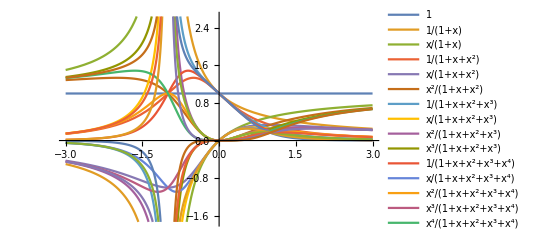

```mathematica
Plot[Evaluate@Table[x^i/Plus@@(x^Range[0,j]),{j,0,5},{i,0,j}],{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Square
```